```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/scratch/nelson/Heterostructure

## System with size (xsize)*(ysize)

```mathematica
T=20;
xsize=50;
ysize=30;
homcond=Import["Drudeweightoffield/Tdepscat/T"<>ToString[T]<>"cJ/drudeweightxsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"fieldsize0.dat"];
For[l=0,l≤xsize,l=l+2,
hetcond=Import["Drudeweightoffield/Tdepscat/T"<>ToString[T]<>"cJ/drudeweightxsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"fieldsize"<>ToString[l]<>".dat"];
ToExpression["normcond"<>ToString[l],InputForm,Function[name,name=Table[{hetcond⟦i⟧⟦1⟧,hetcond⟦i⟧⟦2⟧/homcond⟦1⟧⟦2⟧,0,0,hetcond⟦i⟧⟦5⟧/homcond⟦1⟧⟦5⟧},{i,1,Length[hetcond]}],HoldAll]];
help=ToExpression["normcond"<>ToString[l]];
PrependTo[help,{0,1,0,0,1}];
ToExpression["normcond"<>ToString[l],InputForm,Function[name,name=help,HoldAll]];
]
```

```mathematica
For[d=1,d≤100,d++,
help=Table[Flatten[{l,ToExpression["normcond"<>ToString[l]<>"[[d]][[2;;5]]"]}],{l,0,xsize,2}];
Export["Fancy_plot/Drudeoverl/xsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"/kappaoverlT"<>ToString[T]<>"cJE"<>ToString[d-1]<>"cJ.dat",help,"Data"];
]
```

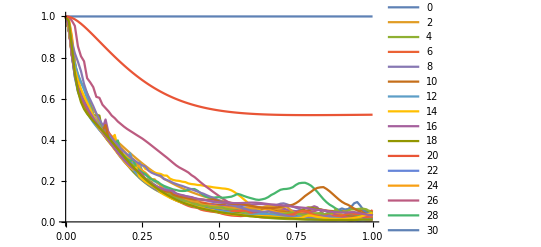

```mathematica
j=2;
ListPlot[Table[Table[{ToExpression["normcond"<>ToString[l]<>"[[i,1]]"],ToExpression["normcond"<>ToString[l]<>"[[i,j]]"]},{i,1,Length[ToExpression["normcond"<>ToString[l]]]}],{l,0,xsize,2}],Joined->True,PlotLegends->Table[i,{i,0,xsize,2}],PlotRange->All]
```

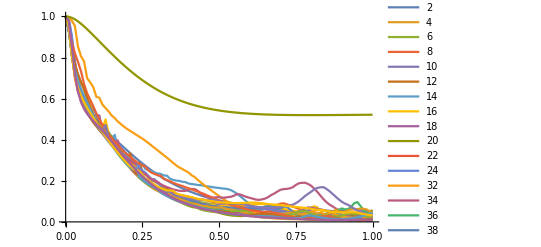

```mathematica
j=2;
ListPlot[{Table[{normcond2⟦i⟧⟦1⟧,normcond2⟦i⟧⟦j⟧},{i,1,Length[normcond2]}],Table[{normcond4⟦i⟧⟦1⟧,normcond4⟦i⟧⟦j⟧},{i,1,Length[normcond4]}],Table[{normcond6⟦i⟧⟦1⟧,normcond6⟦i⟧⟦j⟧},{i,1,Length[normcond6]}],Table[{normcond8⟦i⟧⟦1⟧,normcond8⟦i⟧⟦j⟧},{i,1,Length[normcond8]}],Table[{normcond10⟦i⟧⟦1⟧,normcond10⟦i⟧⟦j⟧},{i,1,Length[normcond10]}],Table[{normcond12⟦i⟧⟦1⟧,normcond12⟦i⟧⟦j⟧},{i,1,Length[normcond12]}],Table[{normcond14⟦i⟧⟦1⟧,normcond14⟦i⟧⟦j⟧},{i,1,Length[normcond14]}],Table[{normcond16⟦i⟧⟦1⟧,normcond16⟦i⟧⟦j⟧},{i,1,Length[normcond16]}],Table[{normcond18⟦i⟧⟦1⟧,normcond18⟦i⟧⟦j⟧},{i,1,Length[normcond18]}],Table[{normcond20⟦i⟧⟦1⟧,normcond20⟦i⟧⟦j⟧},{i,1,Length[normcond20]}],Table[{normcond22⟦i⟧⟦1⟧,normcond22⟦i⟧⟦j⟧},{i,1,Length[normcond22]}],Table[{normcond24⟦i⟧⟦1⟧,normcond24⟦i⟧⟦j⟧},{i,1,Length[normcond24]}],
Table[{normcond26⟦i⟧⟦1⟧,normcond26⟦i⟧⟦j⟧},{i,1,Length[normcond26]}],
Table[{normcond28⟦i⟧⟦1⟧,normcond28⟦i⟧⟦j⟧},{i,1,Length[normcond28]}],
Table[{normcond30⟦i⟧⟦1⟧,normcond30⟦i⟧⟦j⟧},{i,1,Length[normcond30]}],
Table[{normcond32⟦i⟧⟦1⟧,normcond32⟦i⟧⟦j⟧},{i,1,Length[normcond32]}],Table[{normcond34⟦i⟧⟦1⟧,normcond34⟦i⟧⟦j⟧},{i,1,Length[normcond34]}],Table[{normcond36⟦i⟧⟦1⟧,normcond36⟦i⟧⟦j⟧},{i,1,Length[normcond36]}],Table[{normcond38⟦i⟧⟦1⟧,normcond38⟦i⟧⟦j⟧},{i,1,Length[normcond38]}],
Table[{normcond40⟦i⟧⟦1⟧,normcond40⟦i⟧⟦j⟧},{i,1,Length[normcond40]}],
Table[{normcond42⟦i⟧⟦1⟧,normcond42⟦i⟧⟦j⟧},{i,1,Length[normcond42]}],Table[{normcond44⟦i⟧⟦1⟧,normcond44⟦i⟧⟦j⟧},{i,1,Length[normcond44]}],Table[{normcond46⟦i⟧⟦1⟧,normcond46⟦i⟧⟦j⟧},{i,1,Length[normcond46]}],Table[{normcond48⟦i⟧⟦1⟧,normcond48⟦i⟧⟦j⟧},{i,1,Length[normcond48]}],Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦j⟧},{i,1,Length[normcond50]}]},Joined->True,PlotLegends->{2,4,6,8,10,12,14,16,18,20,22,24,32,34,36,38,42,44,46,48,50},PlotRange->All]
```

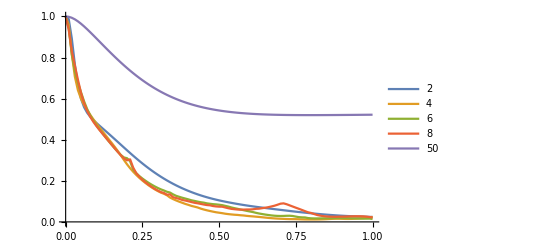

```mathematica
j=2;
ListPlot[{Table[{normcond2⟦i⟧⟦1⟧,normcond2⟦i⟧⟦j⟧},{i,1,Length[normcond2]}],Table[{normcond4⟦i⟧⟦1⟧,normcond4⟦i⟧⟦j⟧},{i,1,Length[normcond4]}],Table[{normcond6⟦i⟧⟦1⟧,normcond6⟦i⟧⟦j⟧},{i,1,Length[normcond6]}],Table[{normcond8⟦i⟧⟦1⟧,normcond8⟦i⟧⟦j⟧},{i,1,Length[normcond8]}],Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦j⟧},{i,1,Length[normcond50]}]},Joined->True,PlotLegends->{2,4,6,8,50},PlotRange->All]
```

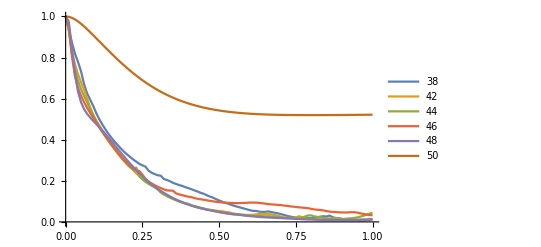

```mathematica
j=2;
ListPlot[{Table[{normcond38⟦i⟧⟦1⟧,normcond38⟦i⟧⟦j⟧},{i,1,Length[normcond38]}],Table[{normcond42⟦i⟧⟦1⟧,normcond42⟦i⟧⟦j⟧},{i,1,Length[normcond42]}],Table[{normcond44⟦i⟧⟦1⟧,normcond44⟦i⟧⟦j⟧},{i,1,Length[normcond44]}],Table[{normcond46⟦i⟧⟦1⟧,normcond46⟦i⟧⟦j⟧},{i,1,Length[normcond46]}],Table[{normcond48⟦i⟧⟦1⟧,normcond48⟦i⟧⟦j⟧},{i,1,Length[normcond48]}],Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦j⟧},{i,1,Length[normcond50]}]},Joined->True,PlotLegends->{38,42,44,46,48,50},PlotRange->All]
```

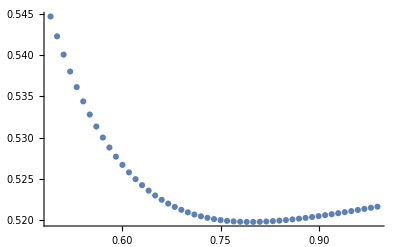

```mathematica
ListPlot[Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦2⟧},{i,50,100}]]
```

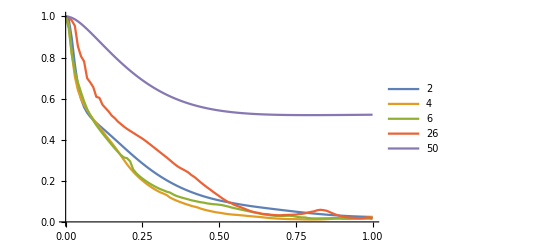

```mathematica
j=2;
ListPlot[{Table[{normcond2⟦i⟧⟦1⟧,normcond2⟦i⟧⟦j⟧},{i,1,Length[normcond2]}],Table[{normcond4⟦i⟧⟦1⟧,normcond4⟦i⟧⟦j⟧},{i,1,Length[normcond4]}],Table[{normcond6⟦i⟧⟦1⟧,normcond6⟦i⟧⟦j⟧},{i,1,Length[normcond6]}],Table[{normcond12⟦i⟧⟦1⟧,normcond26⟦i⟧⟦j⟧},{i,1,Length[normcond12]}],Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦j⟧},{i,1,Length[normcond50]}]},Joined->True,PlotLegends->{2,4,6,26,50},PlotRange->All]
```

```mathematica
j=2;
Manipulate[ListPlot[Table[{l,ToExpression["normcond"<>ToString[l]<>"[["<>ToString[d]<>"]][[j]]"]},{l,0,xsize,2}],Joined->False,PlotRange->All],{d,1,101,1}]
```

```mathematica
Manipulate[ListPlot[{{0,1},{2,normcond2[[d]][[j]]},{4,normcond4[[d]][[j]]},{6,normcond6[[d]][[j]]},{8,normcond8[[d]][[j]]},{10,normcond10[[d]][[j]]},{12,normcond12[[d]][[j]]},{14,normcond14[[d]][[j]]},{16,normcond16[[d]][[j]]},{18,normcond18[[d]][[j]]},{20,normcond20[[d]][[j]]},{22,normcond22[[d]][[j]]},{24,normcond24[[d]][[j]]},{28,normcond28[[d]][[j]]},{30,normcond30[[d]][[j]]},{32,normcond32[[d]][[j]]},{34,normcond34[[d]][[j]]},{36,normcond36[[d]][[j]]},{38,normcond38[[d]][[j]]},{40,normcond40[[d]][[j]]},{42,normcond42[[d]][[j]]},{44,normcond44[[d]][[j]]},{46,normcond46[[d]][[j]]},{48,normcond48[[d]][[j]]},{50,normcond50[[d]][[j]]}},Joined->True,PlotRange->{{0,50},{0,1.1}}],{d,1,100,1}]
```

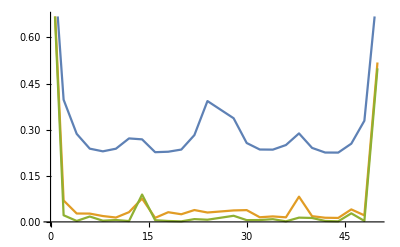

```mathematica
ListPlot[Table[{{0,1},{2,normcond2[[d]][[j]]},{4,normcond4[[d]][[j]]},{6,normcond6[[d]][[j]]},{8,normcond8[[d]][[j]]},{10,normcond10[[d]][[j]]},{12,normcond12[[d]][[j]]},{14,normcond14[[d]][[j]]},{16,normcond16[[d]][[j]]},{18,normcond18[[d]][[j]]},{20,normcond20[[d]][[j]]},{22,normcond22[[d]][[j]]},{24,normcond24[[d]][[j]]},{28,normcond28[[d]][[j]]},{30,normcond30[[d]][[j]]},{32,normcond32[[d]][[j]]},{34,normcond34[[d]][[j]]},{36,normcond36[[d]][[j]]},{38,normcond38[[d]][[j]]},{40,normcond40[[d]][[j]]},{42,normcond42[[d]][[j]]},{44,normcond44[[d]][[j]]},{46,normcond46[[d]][[j]]},{48,normcond48[[d]][[j]]},{50,normcond50[[d]][[j]]}},{d,10,50,20}],Joined->True]
```

```mathematica
T=10;
homcond=Import["Drudeweightoffield/Tdepscat/T"<>ToString[T]<>"cJ/drudeweightxsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"fieldsize"<>ToString[xsize]<>".dat"];
PrependTo[homcond,Import["Drudeweightoffield/Tdepscat/T"<>ToString[T]<>"cJ/drudeweightxsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"fieldsize0.dat"][[1]]];
For[l=0,l≤xsize,l=l+2,
hetcond=Import["Drudeweightoffield/Tdepscat/T"<>ToString[T]<>"cJ/drudeweightxsize"<>ToString[xsize]<>"ysize"<>ToString[ysize]<>"fieldsize"<>ToString[l]<>".dat"];
ToExpression["normcond"<>ToString[l],InputForm,Function[name,name=Table[{hetcond⟦i⟧⟦1⟧,hetcond⟦i⟧⟦2⟧/(((xsize-l)*homcond⟦1⟧⟦2⟧+l*homcond⟦i⟧⟦2⟧)/xsize),0,0,hetcond⟦i⟧⟦5⟧/(((xsize-l)*homcond⟦1⟧⟦5⟧+l*homcond⟦i⟧⟦5⟧)/xsize)},{i,1,Length[hetcond]}],HoldAll]];
help=ToExpression["normcond"<>ToString[l]];
PrependTo[help,{0,1,0,0,1}];
ToExpression["normcond"<>ToString[l],InputForm,Function[name,name=help,HoldAll]];
]
```

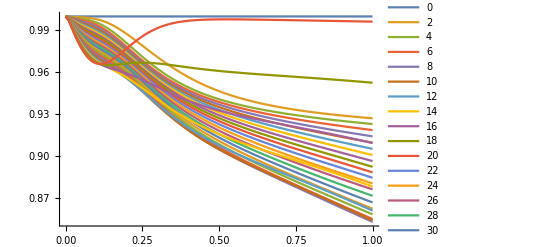

```mathematica
j=5;
ListPlot[Table[Table[{ToExpression["normcond"<>ToString[l]<>"[[i]][[1]]"],ToExpression["normcond"<>ToString[l]<>"[[i]][[j]]"]},{i,1,Length[ToExpression["normcond"<>ToString[l]]]}],{l,0,xsize,2}],Joined->True,PlotLegends->Table[i,{i,0,xsize,2}],PlotRange->All]
```

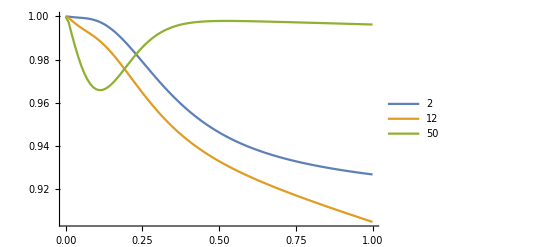

```mathematica
j=5;
ListPlot[{Table[{normcond2⟦i⟧⟦1⟧,normcond2⟦i⟧⟦j⟧},{i,1,Length[normcond2]}],Table[{normcond12⟦i⟧⟦1⟧,normcond12⟦i⟧⟦j⟧},{i,1,Length[normcond12]}],Table[{normcond50⟦i⟧⟦1⟧,normcond50⟦i⟧⟦j⟧},{i,1,Length[normcond50]}]},Joined->True,PlotLegends->{2,12,50},PlotRange->All]
```

```mathematica
Manipulate[ListPlot[Table[{l,ToExpression["normcond"<>ToString[l]<>"[["<>ToString[d]<>"]][[j]]"]},{l,0,50,2}],PlotRange->All,Joined->True],{d,1,101,1}]
```